# A NEURAL NETWORK FOR PNEUMONIA

Raffaele Petrolo
Mat: 252120

Andrò ad addestrare una net su un dataset raggi x al torace di pazienti affetti da polmonite batterica o virale al fine di far riconosere alla net una possibile infezione da polmonite. Ho un dataset composta da 500 immagini di cui 250 appartengono  a pazienti con polmonite e 250 a persone senza polmonite. Utilizzerò la net VGG 16.

NON ELABORARE I CODICI ALTRIMENTI SI CANCELLERANNO LE IMMAGINI!

### PREPARING DATA

```mathematica
CreateLabeledData[folder_,label_]:=Module[{files},files=FileNames["*.jpg",{folder}];
Map[<|"Image"->Import[#],"Label"->label|>&,files]];
```

```mathematica
trainNormal="C:\\Users\\raffy\\Documents\\university\\LM\\1_anno_1_sem\\modellistica\\dataset_polmonite\\train\\Normali_f";
trainPneumonia="C:\\Users\\raffy\\Documents\\university\\LM\\1_anno_1_sem\\modellistica\\dataset_polmonite\\train\\Polmonite_f";
validNormal="C:\\Users\\raffy\\Documents\\university\\LM\\1_anno_1_sem\\modellistica\\dataset_polmonite\\Validation\\Normali_f";
validPneumonia="C:\\Users\\raffy\\Documents\\university\\LM\\1_anno_1_sem\\modellistica\\dataset_polmonite\\Validation\\Polmonite_f";

sickTrainData=CreateLabeledData[trainPneumonia,"Sick"];
healthyTrainData=CreateLabeledData[trainNormal,"Healthy"];
trainDataTemp=Join[sickTrainData,healthyTrainData];

sickValidationData=CreateLabeledData[validPneumonia,"Sick"];
healthyValidationData=CreateLabeledData[validNormal,"Healthy"];
validationDataTemp=Join[sickValidationData,healthyValidationData];
(*Convert training and validation data to the correct format*)
trainData=Map[<|"Input"->#["Image"],"Output"->#["Label"]|>&,trainDataTemp];
validationData=Map[<|"Input"->#["Image"],"Output"->#["Label"]|>&,validationDataTemp];
```

### TRAIN AND SAVE THE MODEL

```mathematica
(*Load the pre-trained VGG16 model*)
vgg16=NetModel["VGG-16 Trained on ImageNet Competition Data"];
(*Define new output layer for binary classification directly*)
modifiedVGG16=NetReplacePart[vgg16,{(*Replace the last fully connected layer to have an output dimension of 2 for binary classification*)
"fc8"->LinearLayer[2],
(*Ensure the output uses a softmax layer for binary classification probabilities*)"prob"->SoftmaxLayer[],
(*Specify the output decoder for binary classification*)"Output"->NetDecoder[{"Class",{"Sick","Healthy"}}]}];
modifiedVGG16=NetReplacePart[modifiedVGG16,"Input"->NetEncoder[{"Image",{224,224},"ColorSpace"->"RGB"}]];
(*NetEncoder formatta le immagini nel formato di input per la VGG ovvero immagini RGB 224*224)
```

```mathematica
(*Training options*)
options={MaxTrainingRounds->50,ValidationSet->validationData,BatchSize->64,TargetDevice->"CPU",LearningRate->0.0001 };
(*Train the model*)
trainedModel=NetTrain[modifiedVGG16,trainData,Sequence@@options]
```

```mathematica
(*save the net*)
Export["C:\\Users\\raffy\\Documents\\university\\LM\\1_anno_1_sem\\modellistica\\Mynet\\trainedModel4.wlnet",trainedModel];
```

### TESTING

#### Preparing testing data

```mathematica
testNormal="C:\\Users\\raffy\\Documents\\university\\LM\\1_anno_1_sem\\modellistica\\dataset_polmonite\\test\\NORMAL_F";
testPneumonia="C:\\Users\\raffy\\Documents\\university\\LM\\1_anno_1_sem\\modellistica\\dataset_polmonite\\test\\PNEUMONIA_F";
sickTestData=CreateLabeledData[testPneumonia,"Sick"];
healthyTestData=CreateLabeledData[testNormal,"Healthy"];
testData=Join[sickTestData,healthyTestData];
```

#### Using my net to generate predictions

```mathematica
(*Generate predictions*)
mynet=Import["C:\\Users\\raffy\\Documents\\university\\LM\\1_anno_1_sem\\modellistica\\Mynet\\trainedModel3.wlnet"]
```

Import::nnincmpb: Attempting to import a network that was produced using version 14.0.2 of the Neural Networks paclet in version 13.3.0. This can cause some issues.

NetChain[<>]

```mathematica
predictions=mynet/@testData[[All,"Image"]];
```

#### Metrics analysis

Accuracy: 0.764423

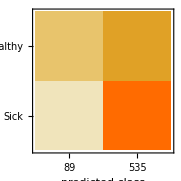

Total patients 624

```mathematica
(*Extract the true labels*)
trueLabels=testData[[All,"Label"]];
(*Calculate accuracy or other performance metrics*)
accuracy=Mean[Boole[#1==#2]&@@@Transpose[{trueLabels,predictions}]];
cm=ClassifierMeasurements[predictions,trueLabels];
confusionMatrixPlot=cm["ConfusionMatrixPlot"];
Print["Accuracy: ",N[accuracy]];
confusionMatrixPlot
Print["Total patients ",Length[testData[[All,"Label"]]]]
```

In ambito medico l’accuratezza non è una metrica indicativa della performance del modello; Per esempio assumiamo di voler realizzare un sistema di intelligena artificiale in grado di rilevare tumore al cervello in un campione di 100 pazienti. Assumiamo di avere nel nostro dataset 100 pazienti di cui 99 sani e 1 malato, sostanzialemente poichè l’incidenza di tale malattia è bassa e questa potrebbe essere una situation reale. In questo caso un modello di intelligenza artificiale che restitutisce come risposta sano avrà un’accuratezza del 99%, ma di fatto codesta rete risulta completamente inefficace nell’identificazione del cancro. In questo contesto più rilevante è una metrica chiamata precision che misura la percentuale di positivi rilevati dall’intelligenza artificiale rispetto a tutti i positivi e si calcola come:
-Graphics-

```mathematica
truePositive=389;
falsePositive=146;
precision=N[truePositive/(truePositive+falsePositive)]
```

0.727103

Contestualizzando all’esempio precedente, il modello di Intelligenza Artificiale ha come scopo identificare i pazienti affetti da cancro. Dunque, definiremo classe positiva quella dei malati. Essendo pari a 0 il numero di malati classificati come tali dal modello (cioè i veri positivi sono 0), il risultato dell’intera frazione è 0. 
Un’ altra metrica da considerare è la recall la quale mi indica quanti elementi rilevanti (i positivi)  vengono recuperati.

```mathematica
totalPositive=Length[sickTestData[[All,1]]];
falseNegative=1;
recall=N[truePositive/totalPositive]
```

0.997436

Questo paramentro mi indica che la mia net ha imparato bene a riconoscere i malati.

#### Some examples

Preparo quattro esempi, due di persone con polmonite e due sane.

```mathematica
mynet=Import["C:\\Users\\raffy\\Documents\\university\\LM\\1_anno_1_sem\\modellistica\\Mynet\\trainedModel3.wlnet"];
```

Import::nnincmpb: Attempting to import a network that was produced using version 14.0.2 of the Neural Networks paclet in version 13.3.0. This can cause some issues.

```mathematica
Print["\nEsempio di persona affetta da polmonite\n"]
firstExample=sickTestData[[1,1]]
Print["\nEsempio di persona affetta da polmonite\n"]
secondExample=sickTestData[[102,1]]
Print["\nEsempio di persona sana\n"]
thirdExample=healthyTestData[[56,1]]
Print["\nEsempio di persona sana\n"]
lastExample=healthyTestData[[97,1]]
```

Esempio di persona affetta da polmonite

-Graphics-

Esempio di persona affetta da polmonite

-Graphics-

Esempio di persona sana

-Graphics-

Esempio di persona sana

-Graphics-

```mathematica
mynet[firstExample]
mynet[secondExample]
mynet[thirdExample]
mynet[lastExample]
```

Sick

Sick

Healthy

Healthy

In questo caso ha individuato correttamente tutti i pazienti affetti da polmonite e chi no. Fallisce in alcuni casi, infatti ha un’accuracy del 76%, come ad esempio:

```mathematica
mynet[healthyTestData[[98,1]]]
healthyTestData[[98,1]]
```

Sick

-Graphics-

In questo caso da come affetto da malattia una persona sana.